```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->15};
d=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/1.3_1_log.lammps","Table"],49,0],-27,0]];
```

```mathematica
Mean[d[[2]]]
```

6.63949

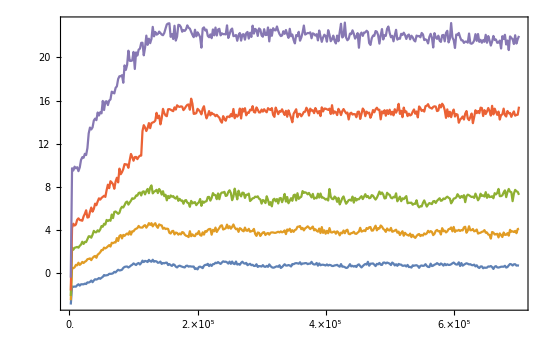

```mathematica
bmin=0;
bmax=700000;
p1=ListLinePlot[{Table[{i*2000,d2[[2]][[i]]},{i,Length[d2[[2]]]}],Table[{i*2000,d3[[2]][[i]]},{i,Length[d3[[2]]]}],Table[{i*2000,d[[2]][[i]]},{i,Length[d[[2]]]}],Table[{i*2000,d4[[2]][[i]]},{i,Length[d4[[2]]]}],Table[{i*2000,d5[[2]][[i]]},{i,Length[d5[[2]]]}]},PlotRange->All,FrameLabel->{MaTeX["\\text{Time }t",Magnification->2],MaTeX["\\text{Pressure }p",Magnification->2]},LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},Frame->True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm[N@i,0]},{i,bmin,bmax,(bmax-bmin)/7}],None}},FrameStyle->Directive[Black,Thickness[0.005]],Epilog->{Inset[MaTeX["(\\text{a})",Magnification->2],Scaled[{0.07,0.9}]]},PlotLegends->{Placed[{MaTeX["T=0.5,\\rho=1",Magnification->2],MaTeX["T=0.9,\\rho=1",Magnification->2],MaTeX["T=1.3,\\rho=1",Magnification->2],MaTeX["T=1.8,\\rho=1",Magnification->2],MaTeX["T=3,\\rho=1",Magnification->2]},Right]},ImageSize->550]
```

```mathematica
d2=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/0.5_1_log.lammps","Table"],49,0],-27,0]];
```

```mathematica
d3=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/0.9_1_log.lammps","Table"],49,0],-27,0]];
```

```mathematica
d4=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/1.8_1_log.lammps","Table"],49,0],-27,0]];
```

```mathematica
d5=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/3_1_log.lammps","Table"],49,0],-27,0]];
```

```mathematica
Export["~/Desktop/Study Related/大四上/计算物理/class_2_s/Fig1.pdf",p1]
```

~/Desktop/Study Related/大四上/计算物理/class_2_s/Fig1.pdf

```mathematica
s1=Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/T0.5/rho2.0.lammps","Table"],49,0],-27,0]];
```

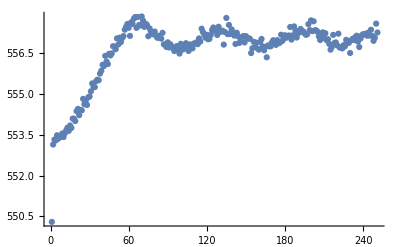

```mathematica
ListPlot[s1[[2]],PlotRange->All]
```

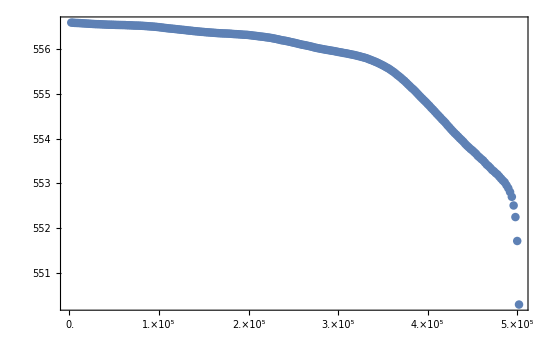

```mathematica
ListPlot[Table[Mean[Table[{2000*(j),s1[[2]][[i-j+1]]},{i,j,Length[s1[[2]]]}]],{j,Length[s1[[2]]]}],PlotRange->All,FrameLabel->{MaTeX["\\text{Time }t",Magnification->2],MaTeX["\\text{Average pressure }Q(t)",Magnification->2]},LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},Frame->True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm[N@i,0]},{i,0,500000,100000}],None}},Epilog->{Inset[MaTeX["(\\text{a})",Magnification->2],Scaled[{0.07,0.9}]]},FrameStyle->Directive[Black,Thickness[0.005]],ImageSize->550]
```

```mathematica
MeanDeviation[Table[Mean[Table[s1[[2]][[i-j+1]],{i,j,Length[s1[[2]]]}]],{j,Length[s1[[2]]]}]]/Mean[s1[[2]]]
```

0.00161451

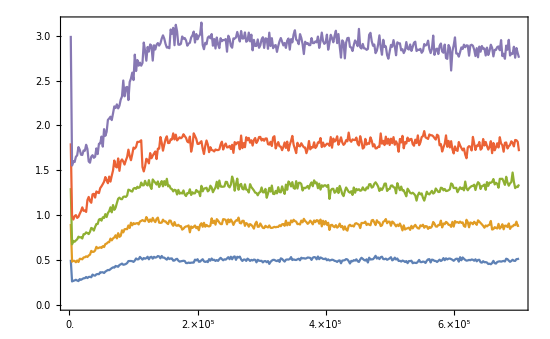

```mathematica
p2=ListLinePlot[{Table[{i*2000,d2[[4]][[i]]},{i,Length[d2[[2]]]}],Table[{i*2000,d3[[4]][[i]]},{i,Length[d3[[2]]]}],Table[{i*2000,d[[4]][[i]]},{i,Length[d[[2]]]}],Table[{i*2000,d4[[4]][[i]]},{i,Length[d4[[2]]]}],Table[{i*2000,d5[[4]][[i]]},{i,Length[d5[[2]]]}]},PlotRange->All,FrameLabel->{MaTeX["\\text{Time }t",Magnification->2],MaTeX["\\text{Temperature }T",Magnification->2]},LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},Frame->True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm[N@i,0]},{i,bmin,bmax,(bmax-bmin)/7}],None}},FrameStyle->Directive[Black,Thickness[0.005]],Epilog->{Inset[MaTeX["(\\text{b})",Magnification->2],Scaled[{0.07,0.9}]]},PlotLegends->{Placed[{MaTeX["T=0.5,\\rho=1",Magnification->2],MaTeX["T=0.9,\\rho=1",Magnification->2],MaTeX["T=1.3,\\rho=1",Magnification->2],MaTeX["T=1.8,\\rho=1",Magnification->2],MaTeX["T=3,\\rho=1",Magnification->2]},Right]},ImageSize->550]
```

```mathematica
Export["~/Desktop/Study Related/大四上/计算物理/class_2_s/Fig2.pdf",p2]
```

~/Desktop/Study Related/大四上/计算物理/class_2_s/Fig2.pdf

```mathematica
Charting`ResolvePlotTheme[Automatic,Plot]
```

{GridLinesStyle→Directive[-Graphics-],Method→{AxisPadding→Scaled[0.02],DefaultBoundaryStyle→Automatic,DefaultPlotStyle→{Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]],Directive[-Graphics-,AbsoluteThickness[1.6]]},DomainPadding→Scaled[0.02],RangePadding→Scaled[0.05]}}

```mathematica
MeanDeviation[Table[Mean[Table[s16[[2]][[i-j+1]],{i,j,Length[s16[[2]]]}]],{j,Length[s16[[2]]]}]]/Mean[s16[[2]]]
```

-0.418957

```mathematica
f[z_]:=MeanDeviation[Table[Mean[Table[z[[2]][[i-j+1]],{i,j,Length[z[[2]]]}]],{j,Length[z[[2]]]}]]/Mean[z[[2]]]
```

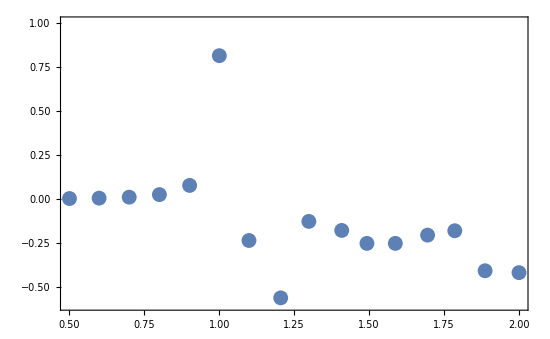

```mathematica
ListPlot[{{1/2.0,f[s1]},{1/1.43,f[s8]},{1/1.67,f[s2]},{1/1.25,f[s3]},{1/1.11,f[s9]},{1/1.0,f[s4]},{1/0.91,f[s10]},{1/0.83,f[s5]},{1/0.77,f[s11]},{1/0.71,f[s6]},{1/0.67,f[s12]},{1/0.63,f[s12]},{1/0.59,f[s13]},{1/0.56,f[s14]},{1/0.53,f[s15]},{1/0.5,f[s16]}},PlotRange->{{0.5,2},{-0.6,1}},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.005]],Epilog->{Inset[MaTeX["(\\text{b})",Magnification->2],Scaled[{0.07,0.9}]],Inset[p3,Scaled[{0.7,0.66}]]},FrameLabel->{MaTeX["\\text{Volume }V",Magnification->2],MaTeX["\\text{Validity }v",Magnification->2]},ImageSize->550]
```

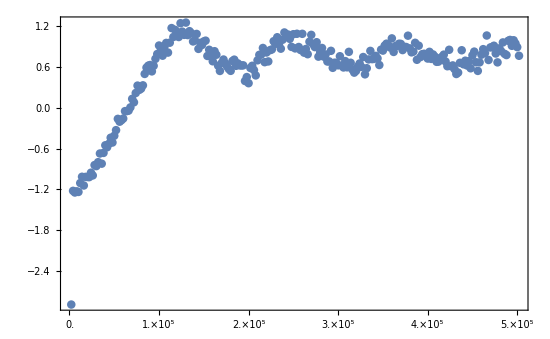

```mathematica
ListPlot[Table[{2000*i,s4[[2]][[i]]},{i,Length[s4[[2]]]}],PlotRange->All,FrameLabel->{MaTeX["\\text{Time }t",Magnification->2],MaTeX["\\text{Pressure }p",Magnification->2]},LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},Frame->True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm[N@i,0]},{i,0,500000,100000}],None}},Epilog->{Inset[MaTeX["(\\text{c})",Magnification->2],Scaled[{0.07,0.9}]]},FrameStyle->Directive[Black,Thickness[0.005]],ImageSize->550]
```

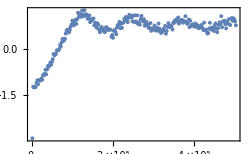

```mathematica
p3=ListPlot[Table[{2000*i,s4[[2]][[i]]},{i,Length[s4[[2]]]}],PlotRange->All,FrameLabel->{MaTeX["\\text{Time }t",Magnification->2],MaTeX["\\text{Pressure }p",Magnification->2]},LabelStyle->{FontFamily->"Latin Modern Roman",Black,10},Frame->True,FrameTicks->{{Automatic,None},{Table[{i,ScientificForm[N@i,0]},{i,0,500000,100000}],None}},FrameStyle->Directive[Black,Thickness[0.005]],ImageSize->250]
```

```mathematica
space={0.95,0.87,0.93,0.89,0.88,0.885,0.881,0.905,0.903,0.84,0.85,0.86,0.82,0.81,0.8,0.79,0.78};
For[i=5,i≤20,i++,AppendTo[space,Round[1000/i]/100]]
space=Sort[space];
For[i=1,i<=Length[space],i++,If[Element[space[[i]],Integers],space[[i]]=ToString[IntegerPart[space[[i]]]]<>".0"]]
space[[5]]=0.63;
temp={0.5, 0.9, 1.3, 1.8};
ff=Table[Table[Transpose[Drop[Drop[Import["~/Desktop/Study Related/大四上/计算物理/class_2_s/T"<>ToString[temp[[j]]]<>"/rho"<>ToString[N[space[[i]]]]<>".lammps","Table"],49,0],-27,0]],{i,Length[space]}],{j,Length[temp]}];
```

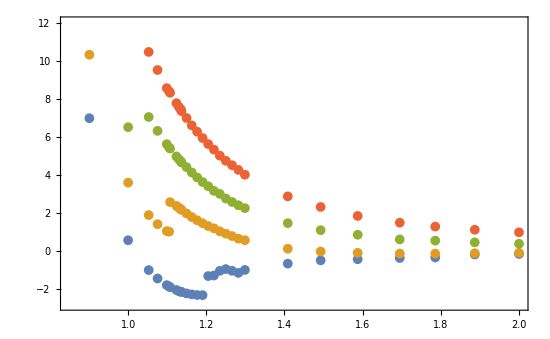

```mathematica
Needs["PlotLegends`"];
ListPlot[Table[Table[{1/ToExpression[N[space[[i]]]],Mean[ff[[j]][[i]][[2]]]},{i,Length[ff[[j]]]}],{j,Length[temp]}],PlotRange->{{0.85,2},{-2.8,12}},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",Black,17},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\text{Volume }V",Magnification->2],MaTeX["\\text{Pressure }p",Magnification->2]},PlotStyle->AbsolutePointSize[7],Epilog->{Inset[MaTeX["(\\text{b})",Magnification->2],Scaled[{0.9,0.9}]]},PlotLegends->{Placed[Table[MaTeX["T="<>ToString[temp[[j]]],Magnification->2],{j,Length[temp]}],Right]},ImageSize->550]
```

```mathematica
Format[TableForm[{N[space]}],TeXForm]
```

\begin{array}{ccccccccccccccccccccccccccccccccc}
 0.5 & 0.53 & 0.56 & 0.59 & 0.63 & 0.67 & 0.71 & 0.77 & 0.78 & 0.79 & 0.8 & 0.81 & 0.82 & 0.83 & 0.84 & 0.85 & 0.86 & 0.87 & 0.88 & 0.881 & 0.885 & 0.89 & 0.903 & 0.905 & 0.91 & 0.93 & 0.95 & 1.0 & 1.11 & 1.25 & 1.43 & 1.67 & 2.0 \\
\end{array}